```mathematica
ClearAll["Global`*"]
```

```mathematica
tag ={"#boston","#bostonmarathon","#bostonstrong","#prayforboston"};
S[x_]:=StringSplit[StringReplace[x,{"\""->""}]," -> "];
Fdate[x_]:=DateString[{2013,4,15,(5+x),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}];
```

```mathematica
L=96;
For[n=1,n≤4,n++,
For[i=1,i≤L,i++,

file="/Users/danielgladstone/Documents/twitter_project/auto_graphing/"<>tag[[n]]<>"1039"<>"/"<>Fdate[i];

If[FileExistsQ[file],

F =Import[file,"List"];

GList[tag[[n]]][i]=DeleteDuplicates[Table[
joined=First[S[F[[j]]]]->Last[S[F[[j]]]]
,{j,1,Length[F]}]];
If[Length[GList[tag[[n]]][i]]==0,
G[tag[[n]]][i]=0;
G[VC][tag[[n]]][i]=0;
G[VID][tag[[n]]][i]=0;
G[CC][tag[[n]]][i]=0;
G[GD][tag[[n]]][i]=0;
G[GR][tag[[n]]][i]=0;
G[GCC][tag[[n]]][i]=0;
G[GA][tag[[n]]][i]=0;
G[MND][tag[[n]]][i]=0;
G[MDC][tag[[n]]][i]=0;,
(*Print["Hashtag is"<>tag[[n]]<>". File is"<>DateString[{2013,4,15,(5+i),0,0},{"DayNameShort","Hour12","AMPMLowerCase"}]<>"."];*)
G[tag[[n]]][i]=Graph[GList[tag[[n]]][i]];
G[VC][tag[[n]]][i]=VertexCount[G[tag[[n]]][i]];
G[VID][tag[[n]]][i]=Mean[VertexInDegree[G[tag[[n]]][i]]];
G[CC][tag[[n]]][i]=Mean[ClosenessCentrality[G[tag[[n]]][i]]];
G[GD][tag[[n]]][i]=GraphDensity[G[tag[[n]]][i]];
G[GR][tag[[n]]][i]=GraphReciprocity[G[tag[[n]]][i]];
G[GCC][tag[[n]]][i]=GlobalClusteringCoefficient[G[tag[[n]]][i]];
G[GA][tag[[n]]][i]=GraphAssortativity[G[tag[[n]]][i]];
G[MND][tag[[n]]][i]=Mean[MeanNeighborDegree[G[tag[[n]]][i]]];
G[MDC][tag[[n]]][i]=Mean[MeanDegreeConnectivity[G[tag[[n]]][i]]];
];
,Continue[]];
]]
```

```mathematica
type={VC,VID,CC,GD,GR,GCC,GA,MND,MDC};
For[p=1,p≤9,p++,
GType=type[[p]];
data=Table[
Table[
G[GType][tag[[n]]][i],{i,L}]
,{n,1,4}(*slect what hashtags to see here i.e.#prayforboston is (n,4,4)*)
];
d[type[[p]]]=data;
]
```

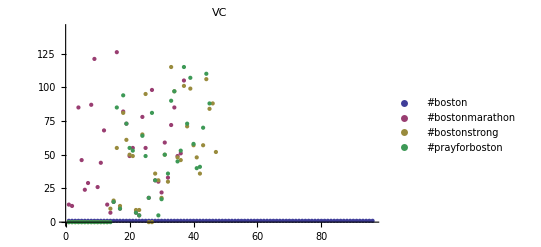
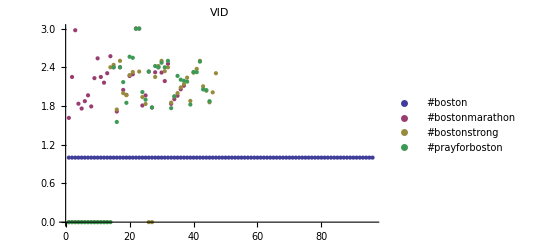
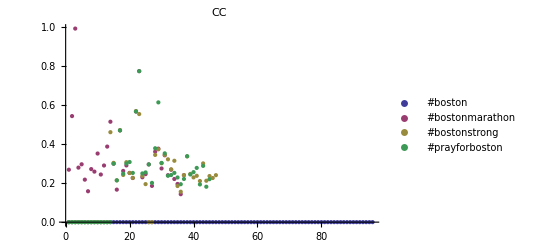
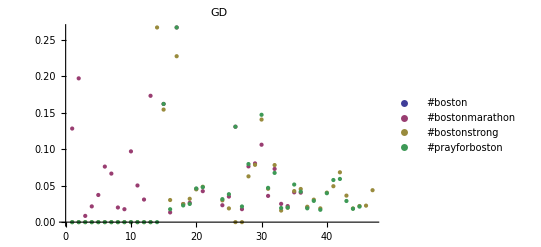
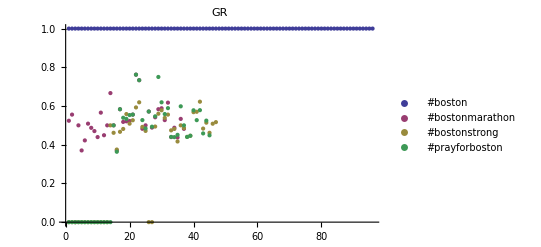
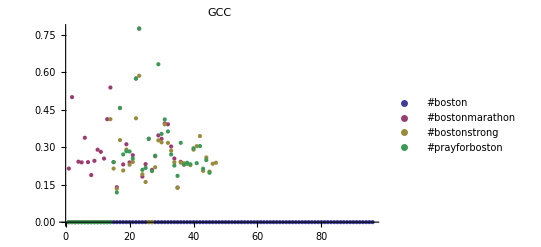
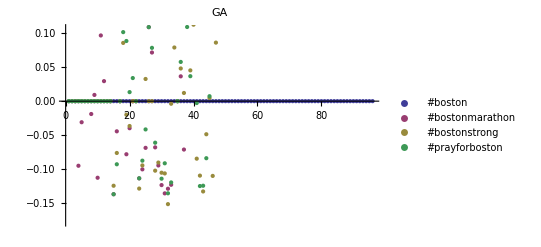
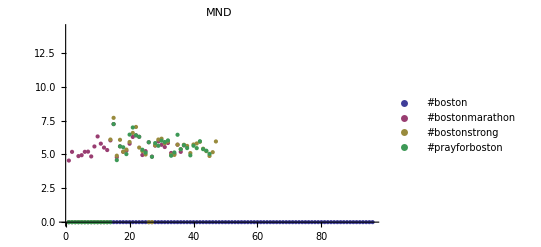

{1.+3.24568×10^-18 x,0.102062 (641.519+0.169745 G[VC][#bostonmarathon][38]+0.163299 G[VC][#bostonmarathon][39]+0.156853 G[VC][#bostonmarathon][40]+0.150407 G[VC][#bostonmarathon][41]+0.143961 G[VC][#bostonmarathon][42]+0.137515 G[VC][#bostonmarathon][43]+0.131069 G[VC][#bostonmarathon][44]+0.124623 G[VC][#bostonmarathon][45]+0.118177 G[VC][#bostonmarathon][46]+0.111731 G[VC][#bostonmarathon][47]+0.105285 G[VC][#bostonmarathon][48]+0.0988391 G[VC][#bostonmarathon][49]+0.092393 G[VC][#bostonmarathon][50]+0.085947 G[VC][#bostonmarathon][51]+0.079501 G[VC][#bostonmarathon][52]+0.073055 G[VC][#bostonmarathon][53]+0.0666089 G[VC][#bostonmarathon][54]+0.0601629 G[VC][#bostonmarathon][55]+0.0537169 G[VC][#bostonmarathon][56]+0.0472709 G[VC][#bostonmarathon][57]+0.0408248 G[VC][#bostonmarathon][58]+0.0343788 G[VC][#bostonmarathon][59]+0.0279328 G[VC][#bostonmarathon][60]+0.0214868 G[VC][#bostonmarathon][61]+0.0150407 G[VC][#bostonmarathon][62]+0.0085947 G[VC][#bostonmarathon][63]+0.00214868 G[VC][#bostonmarathon][64]-0.00429735 G[VC][#bostonmarathon][65]-0.0107434 G[VC][#bostonmarathon][66]-0.0171894 G[VC][#bostonmarathon][67]-0.0236354 G[VC][#bostonmarathon][68]-0.0300815 G[VC][#bostonmarathon][69]-0.0365275 G[VC][#bostonmarathon][70]-0.0429735 G[VC][#bostonmarathon][71]-0.0494195 G[VC][#bostonmarathon][72]-0.0558656 G[VC][#bostonmarathon][73]-0.0623116 G[VC][#bostonmarathon][74]-0.0687576 G[VC][#bostonmarathon][75]-0.0752036 G[VC][#bostonmarathon][76]-0.0816497 G[VC][#bostonmarathon][77]-0.0880957 G[VC][#bostonmarathon][78]-0.0945417 G[VC][#bostonmarathon][79]-0.100988 G[VC][#bostonmarathon][80]-0.107434 G[VC][#bostonmarathon][81]-0.11388 G[VC][#bostonmarathon][82]-0.120326 G[VC][#bostonmarathon][83]-0.126772 G[VC][#bostonmarathon][84]-0.133218 G[VC][#bostonmarathon][85]-0.139664 G[VC][#bostonmarathon][86]-0.14611 G[VC][#bostonmarathon][87]-0.152556 G[VC][#bostonmarathon][88]-0.159002 G[VC][#bostonmarathon][89]-0.165448 G[VC][#bostonmarathon][90]-0.171894 G[VC][#bostonmarathon][91]-0.17834 G[VC][#bostonmarathon][92]-0.184786 G[VC][#bostonmarathon][93]-0.191232 G[VC][#bostonmarathon][94]-0.197678 G[VC][#bostonmarathon][95]-0.204124 G[VC][#bostonmarathon][96])+0.00182716 x (-488.241-0.0779522 G[VC][#bostonmarathon][38]-0.0705282 G[VC][#bostonmarathon][39]-0.0631042 G[VC][#bostonmarathon][40]-0.0556802 G[VC][#bostonmarathon][41]-0.0482561 G[VC][#bostonmarathon][42]-0.0408321 G[VC][#bostonmarathon][43]-0.0334081 G[VC][#bostonmarathon][44]-0.0259841 G[VC][#bostonmarathon][45]-0.0185601 G[VC][#bostonmarathon][46]-0.011136 G[VC][#bostonmarathon][47]-0.00371201 G[VC][#bostonmarathon][48]+0.00371201 G[VC][#bostonmarathon][49]+0.011136 G[VC][#bostonmarathon][50]+0.0185601 G[VC][#bostonmarathon][51]+0.0259841 G[VC][#bostonmarathon][52]+0.0334081 G[VC][#bostonmarathon][53]+0.0408321 G[VC][#bostonmarathon][54]+0.0482561 G[VC][#bostonmarathon][55]+0.0556802 G[VC][#bostonmarathon][56]+0.0631042 G[VC][#bostonmarathon][57]+0.0705282 G[VC][#bostonmarathon][58]+0.0779522 G[VC][#bostonmarathon][59]+0.0853762 G[VC][#bostonmarathon][60]+0.0928003 G[VC][#bostonmarathon][61]+0.100224 G[VC][#bostonmarathon][62]+0.107648 G[VC][#bostonmarathon][63]+0.115072 G[VC][#bostonmarathon][64]+0.122496 G[VC][#bostonmarathon][65]+0.12992 G[VC][#bostonmarathon][66]+0.137344 G[VC][#bostonmarathon][67]+0.144768 G[VC][#bostonmarathon][68]+0.152192 G[VC][#bostonmarathon][69]+0.159616 G[VC][#bostonmarathon][70]+0.16704 G[VC][#bostonmarathon][71]+0.174464 G[VC][#bostonmarathon][72]+0.181889 G[VC][#bostonmarathon][73]+0.189313 G[VC][#bostonmarathon][74]+0.196737 G[VC][#bostonmarathon][75]+0.204161 G[VC][#bostonmarathon][76]+0.211585 G[VC][#bostonmarathon][77]+0.219009 G[VC][#bostonmarathon][78]+0.226433 G[VC][#bostonmarathon][79]+0.233857 G[VC][#bostonmarathon][80]+0.241281 G[VC][#bostonmarathon][81]+0.248705 G[VC][#bostonmarathon][82]+0.256129 G[VC][#bostonmarathon][83]+0.263553 G[VC][#bostonmarathon][84]+0.270977 G[VC][#bostonmarathon][85]+0.278401 G[VC][#bostonmarathon][86]+0.285825 G[VC][#bostonmarathon][87]+0.293249 G[VC][#bostonmarathon][88]+0.300673 G[VC][#bostonmarathon][89]+0.308097 G[VC][#bostonmarathon][90]+0.315521 G[VC][#bostonmarathon][91]+0.322945 G[VC][#bostonmarathon][92]+0.330369 G[VC][#bostonmarathon][93]+0.337793 G[VC][#bostonmarathon][94]+0.345217 G[VC][#bostonmarathon][95]+0.352641 G[VC][#bostonmarathon][96]),0.102062 (356.871+0.105285 G[VC][#bostonstrong][48]+0.0988391 G[VC][#bostonstrong][49]+0.092393 G[VC][#bostonstrong][50]+0.085947 G[VC][#bostonstrong][51]+0.079501 G[VC][#bostonstrong][52]+0.073055 G[VC][#bostonstrong][53]+0.0666089 G[VC][#bostonstrong][54]+0.0601629 G[VC][#bostonstrong][55]+0.0537169 G[VC][#bostonstrong][56]+0.0472709 G[VC][#bostonstrong][57]+0.0408248 G[VC][#bostonstrong][58]+0.0343788 G[VC][#bostonstrong][59]+0.0279328 G[VC][#bostonstrong][60]+0.0214868 G[VC][#bostonstrong][61]+0.0150407 G[VC][#bostonstrong][62]+0.0085947 G[VC][#bostonstrong][63]+0.00214868 G[VC][#bostonstrong][64]-0.00429735 G[VC][#bostonstrong][65]-0.0107434 G[VC][#bostonstrong][66]-0.0171894 G[VC][#bostonstrong][67]-0.0236354 G[VC][#bostonstrong][68]-0.0300815 G[VC][#bostonstrong][69]-0.0365275 G[VC][#bostonstrong][70]-0.0429735 G[VC][#bostonstrong][71]-0.0494195 G[VC][#bostonstrong][72]-0.0558656 G[VC][#bostonstrong][73]-0.0623116 G[VC][#bostonstrong][74]-0.0687576 G[VC][#bostonstrong][75]-0.0752036 G[VC][#bostonstrong][76]-0.0816497 G[VC][#bostonstrong][77]-0.0880957 G[VC][#bostonstrong][78]-0.0945417 G[VC][#bostonstrong][79]-0.100988 G[VC][#bostonstrong][80]-0.107434 G[VC][#bostonstrong][81]-0.11388 G[VC][#bostonstrong][82]-0.120326 G[VC][#bostonstrong][83]-0.126772 G[VC][#bostonstrong][84]-0.133218 G[VC][#bostonstrong][85]-0.139664 G[VC][#bostonstrong][86]-0.14611 G[VC][#bostonstrong][87]-0.152556 G[VC][#bostonstrong][88]-0.159002 G[VC][#bostonstrong][89]-0.165448 G[VC][#bostonstrong][90]-0.171894 G[VC][#bostonstrong][91]-0.17834 G[VC][#bostonstrong][92]-0.184786 G[VC][#bostonstrong][93]-0.191232 G[VC][#bostonstrong][94]-0.197678 G[VC][#bostonstrong][95]-0.204124 G[VC][#bostonstrong][96])+0.00182716 x (-201.547-0.00371201 G[VC][#bostonstrong][48]+0.00371201 G[VC][#bostonstrong][49]+0.011136 G[VC][#bostonstrong][50]+0.0185601 G[VC][#bostonstrong][51]+0.0259841 G[VC][#bostonstrong][52]+0.0334081 G[VC][#bostonstrong][53]+0.0408321 G[VC][#bostonstrong][54]+0.0482561 G[VC][#bostonstrong][55]+0.0556802 G[VC][#bostonstrong][56]+0.0631042 G[VC][#bostonstrong][57]+0.0705282 G[VC][#bostonstrong][58]+0.0779522 G[VC][#bostonstrong][59]+0.0853762 G[VC][#bostonstrong][60]+0.0928003 G[VC][#bostonstrong][61]+0.100224 G[VC][#bostonstrong][62]+0.107648 G[VC][#bostonstrong][63]+0.115072 G[VC][#bostonstrong][64]+0.122496 G[VC][#bostonstrong][65]+0.12992 G[VC][#bostonstrong][66]+0.137344 G[VC][#bostonstrong][67]+0.144768 G[VC][#bostonstrong][68]+0.152192 G[VC][#bostonstrong][69]+0.159616 G[VC][#bostonstrong][70]+0.16704 G[VC][#bostonstrong][71]+0.174464 G[VC][#bostonstrong][72]+0.181889 G[VC][#bostonstrong][73]+0.189313 G[VC][#bostonstrong][74]+0.196737 G[VC][#bostonstrong][75]+0.204161 G[VC][#bostonstrong][76]+0.211585 G[VC][#bostonstrong][77]+0.219009 G[VC][#bostonstrong][78]+0.226433 G[VC][#bostonstrong][79]+0.233857 G[VC][#bostonstrong][80]+0.241281 G[VC][#bostonstrong][81]+0.248705 G[VC][#bostonstrong][82]+0.256129 G[VC][#bostonstrong][83]+0.263553 G[VC][#bostonstrong][84]+0.270977 G[VC][#bostonstrong][85]+0.278401 G[VC][#bostonstrong][86]+0.285825 G[VC][#bostonstrong][87]+0.293249 G[VC][#bostonstrong][88]+0.300673 G[VC][#bostonstrong][89]+0.308097 G[VC][#bostonstrong][90]+0.315521 G[VC][#bostonstrong][91]+0.322945 G[VC][#bostonstrong][92]+0.330369 G[VC][#bostonstrong][93]+0.337793 G[VC][#bostonstrong][94]+0.345217 G[VC][#bostonstrong][95]+0.352641 G[VC][#bostonstrong][96]),0.102062 (362.372+0.118177 G[VC][#prayforboston][46]+0.111731 G[VC][#prayforboston][47]+0.105285 G[VC][#prayforboston][48]+0.0988391 G[VC][#prayforboston][49]+0.092393 G[VC][#prayforboston][50]+0.085947 G[VC][#prayforboston][51]+0.079501 G[VC][#prayforboston][52]+0.073055 G[VC][#prayforboston][53]+0.0666089 G[VC][#prayforboston][54]+0.0601629 G[VC][#prayforboston][55]+0.0537169 G[VC][#prayforboston][56]+0.0472709 G[VC][#prayforboston][57]+0.0408248 G[VC][#prayforboston][58]+0.0343788 G[VC][#prayforboston][59]+0.0279328 G[VC][#prayforboston][60]+0.0214868 G[VC][#prayforboston][61]+0.0150407 G[VC][#prayforboston][62]+0.0085947 G[VC][#prayforboston][63]+0.00214868 G[VC][#prayforboston][64]-0.00429735 G[VC][#prayforboston][65]-0.0107434 G[VC][#prayforboston][66]-0.0171894 G[VC][#prayforboston][67]-0.0236354 G[VC][#prayforboston][68]-0.0300815 G[VC][#prayforboston][69]-0.0365275 G[VC][#prayforboston][70]-0.0429735 G[VC][#prayforboston][71]-0.0494195 G[VC][#prayforboston][72]-0.0558656 G[VC][#prayforboston][73]-0.0623116 G[VC][#prayforboston][74]-0.0687576 G[VC][#prayforboston][75]-0.0752036 G[VC][#prayforboston][76]-0.0816497 G[VC][#prayforboston][77]-0.0880957 G[VC][#prayforboston][78]-0.0945417 G[VC][#prayforboston][79]-0.100988 G[VC][#prayforboston][80]-0.107434 G[VC][#prayforboston][81]-0.11388 G[VC][#prayforboston][82]-0.120326 G[VC][#prayforboston][83]-0.126772 G[VC][#prayforboston][84]-0.133218 G[VC][#prayforboston][85]-0.139664 G[VC][#prayforboston][86]-0.14611 G[VC][#prayforboston][87]-0.152556 G[VC][#prayforboston][88]-0.159002 G[VC][#prayforboston][89]-0.165448 G[VC][#prayforboston][90]-0.171894 G[VC][#prayforboston][91]-0.17834 G[VC][#prayforboston][92]-0.184786 G[VC][#prayforboston][93]-0.191232 G[VC][#prayforboston][94]-0.197678 G[VC][#prayforboston][95]-0.204124 G[VC][#prayforboston][96])+0.00182716 x (-213.407-0.0185601 G[VC][#prayforboston][46]-0.011136 G[VC][#prayforboston][47]-0.00371201 G[VC][#prayforboston][48]+0.00371201 G[VC][#prayforboston][49]+0.011136 G[VC][#prayforboston][50]+0.0185601 G[VC][#prayforboston][51]+0.0259841 G[VC][#prayforboston][52]+0.0334081 G[VC][#prayforboston][53]+0.0408321 G[VC][#prayforboston][54]+0.0482561 G[VC][#prayforboston][55]+0.0556802 G[VC][#prayforboston][56]+0.0631042 G[VC][#prayforboston][57]+0.0705282 G[VC][#prayforboston][58]+0.0779522 G[VC][#prayforboston][59]+0.0853762 G[VC][#prayforboston][60]+0.0928003 G[VC][#prayforboston][61]+0.100224 G[VC][#prayforboston][62]+0.107648 G[VC][#prayforboston][63]+0.115072 G[VC][#prayforboston][64]+0.122496 G[VC][#prayforboston][65]+0.12992 G[VC][#prayforboston][66]+0.137344 G[VC][#prayforboston][67]+0.144768 G[VC][#prayforboston][68]+0.152192 G[VC][#prayforboston][69]+0.159616 G[VC][#prayforboston][70]+0.16704 G[VC][#prayforboston][71]+0.174464 G[VC][#prayforboston][72]+0.181889 G[VC][#prayforboston][73]+0.189313 G[VC][#prayforboston][74]+0.196737 G[VC][#prayforboston][75]+0.204161 G[VC][#prayforboston][76]+0.211585 G[VC][#prayforboston][77]+0.219009 G[VC][#prayforboston][78]+0.226433 G[VC][#prayforboston][79]+0.233857 G[VC][#prayforboston][80]+0.241281 G[VC][#prayforboston][81]+0.248705 G[VC][#prayforboston][82]+0.256129 G[VC][#prayforboston][83]+0.263553 G[VC][#prayforboston][84]+0.270977 G[VC][#prayforboston][85]+0.278401 G[VC][#prayforboston][86]+0.285825 G[VC][#prayforboston][87]+0.293249 G[VC][#prayforboston][88]+0.300673 G[VC][#prayforboston][89]+0.308097 G[VC][#prayforboston][90]+0.315521 G[VC][#prayforboston][91]+0.322945 G[VC][#prayforboston][92]+0.330369 G[VC][#prayforboston][93]+0.337793 G[VC][#prayforboston][94]+0.345217 G[VC][#prayforboston][95]+0.352641 G[VC][#prayforboston][96])}

Plot::plln: Limiting value Min[0, G[VC]["#bostonmarathon"][38], G[VC]["#bostonmarathon"][39], G[VC]["#bostonmarathon"][40], G[VC]["#bostonmarathon"][41], G[VC]["#bostonmarathon"][42], G[VC]["#bostonmarathon"][43], G[VC]["#bostonmarathon"][44], « 36 », G[VC]["#bostonmarathon"][81], G[VC]["#bostonmarathon"][82], G[VC]["#bostonmarathon"][83], G[VC]["#bostonmarathon"][84], G[VC]["#bostonmarathon"][85], G[VC]["#bostonmarathon"][86], « 110 »] in {x, min, max} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},Plot[md,{x,min,max}]]

```mathematica
lp=Table[ListPlot[d[type[[o]]],PlotLabel->type[[o]], PlotLegends->Table[
tag[[t]],{t,1,4}]]
,{o,9}]

md=Table[Fit[d[type[[1]]][[j]],{1,x},x],{j,4}]
min=Min[Table[d[type[[1]]][[j]],{j,4}]];
max = Max[Table[d[type[[1]]][[j]],{j,4}]];

Table[
d[type[[1]]][[j]],{j,4}];

Show[lp,Plot[md,{x,min,max}]]
```

```mathematica
VertexInDegree[G[tag[[3]]][2]]
```

{}

```mathematica
.
```

```mathematica
G=Graph[GList]

VertexCount[G]
Mean[VertexInDegree[G]]
Mean[ClosenessCentrality[G]]
GraphDensity[G]
GraphReciprocity[G]
GlobalClusteringCoefficient[G]
GraphAssortativity[G]
Mean[MeanNeighborDegree[G]]
Mean[MeanDegreeConnectivity[G]]
```

-Graphics-

4

2

0.9375

2/3

3/4

3/5

0

9/2

7/3

```mathematica
First[F[[1]]]->Last[F[[1]]]
```

#cat→#cats

```mathematica
.
```

```mathematica
Table[
Print[i];
,{i,2,5}]
```

2

3

4

5

{Null,Null,Null,Null}